```mathematica
InverseFunction[Sin][1]
```

π/2

```mathematica
approx[lim_]:=With[{step=InverseFunction[Sin][lim]},1/(step lim+π/2-step)]
```

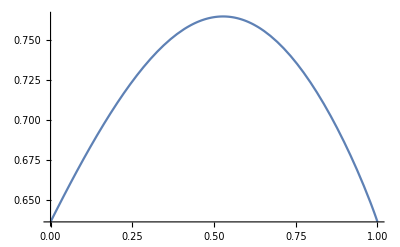

```mathematica
Plot[approx[lim], {lim, 0, 1}]
```

```mathematica
Integrate[Sin[t], {t,0, π/2}]
```

```mathematica
Maximize[approx[lim], lim]//N
```

{0.76438,{lim→0.527766}}

```mathematica
approx[22/40.]
```

0.764098

```mathematica
1/0.76
```

1.31579